# The package VQM`ArgColorPlot

Bernd Thaller
Institute of Mathematics
University of Graz
Austria
2018-04-24

```mathematica
{$Version,Date[]}
```

{11.3.0 for Microsoft Windows (64-bit) (March 7, 2018),{2018,4,25,14,41,40.9068667}}

### Abstract

The package VQM`ArgColorPlot provides methods to visualize complex-valued functions of one real variable. This package is part of the VQM packages which can be obtained here:  https://vqm.uni-graz.at/pages/software.html (free download). The VQM packages are part of the Visual Quantum Mechanics project, see https://vqm.uni-graz.at. In particular, these packages are distributed with the book Advanced Visual Quantum Mechanics, Springer-Verlag New York, 2004.

## Introduction and implementation

Here we describe theoretical background and the practical implementation of the main function in the package VQM`ArgColorPlot`.

### FilledPlot

Filling of a graph can be obtained by

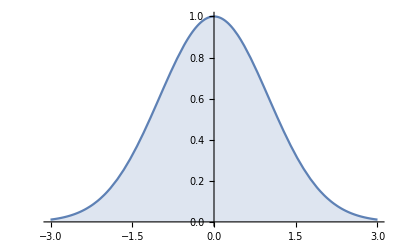

```mathematica
Plot[ⅇ^(-x^2/2),{x,-3,3},Filling->Automatic]
```

```mathematica
Manipulate[Plot[ⅇ^(-x^2/2),{x,-3,3},Filling->Axis,FillingStyle->Hue[c]],{{c,.42,"color"},0,1}]
```

In that way one can produce neat looking graphs.

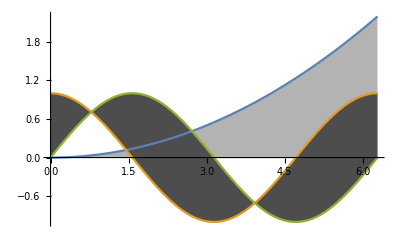

```mathematica
Plot[{x^2/18,Cos[x],Sin[x]},{x,0,2 π},Filling->{2->{{3},{GrayLevel[0.3],GrayLevel[0.3]}},1->Axis},FillingStyle->{GrayLevel[.3],GrayLevel[.7]}]
```

Again, it is only possible to plot real-valued functions.

### Filling with an x-dependent color

In order to visualize a complex-valued function f[x] of one real variable, we use the following idea. We plot the curve Abs[f[x]] and fill the space between the curve and the horizontal axis with a color determined by Arg[f[x]]. Since the argument of a complex number is a real number modulo 2π, it appears natural to choose Hue[Arg[f[x]]/(2π)].

In order to be specific, we define a sample function

```mathematica
f[x_] := Exp[-x^2 + 2 I x]
```

We proceed as follows. First, we define a set of positions on the x-axis and calculate a table of function values at these positions.

```mathematica
xvalues = Table[x,{x,-3.,3.,.1}];
```

(The semicolon serves to suppress the lengthy output). Observe that the boundary values and the increment are given as real numbers. This guarantees that all generated values are real numbers. and when we calculate the value of f for one of these x-values, then Mathematica will return a numeric expression. The function values at these points can be calculated just by applying the function f to the list xvalues:

```mathematica
yvalues = f[xvalues];
```

The variable yvalues now contains a one-dimensional array of complex numbers. With the command Short we can look at an abbreviated form of this expression (The parameter in the command Short describes the desired length of the abbreviated expression). :

```mathematica
Short[yvalues,2]
```

{0.000118494+0.0000344826 ⅈ,0.000197143+0.000103434 ⅈ,0.000305316+0.00024851 ⅈ,«56»,0.000197143-0.000103434 ⅈ,0.000118494-0.0000344826 ⅈ}

Next we generate a table of absolute values

```mathematica
absvals = Abs[yvalues];
```

and a table of arguments

```mathematica
args = Arg[yvalues];
```

From this we want to determine a table of color values. We could try to apply Hue to the list args, but this does not work because Hue is not "listable"

```mathematica
Hue[args/(2 Pi)]    //(Short[#,2]&)
```

Hue[{0.0450703,0.0769013,0.108732,0.140563,0.172394,0.204225,«49»,-0.204225,-0.172394,-0.140563,-0.108732,-0.0769013,-0.0450703}]

We have to use the command Map in order to apply Hue to each of the values in the list. Map has the shortcut /@

```mathematica
Hue /@ (args/(2 Pi))    //(Short[#,2]&)
```

{Hue[0.04507034144862798],Hue[0.07690133006700708],Hue[0.10873231868538617],Hue[0.14056330730376512],Hue[0.17239429592214423],Hue[0.20422528454052333],Hue[0.23605627315890243],Hue[0.2678872617772815],Hue[0.29971825039566047],Hue[0.33154923901403954],Hue[0.36338022763241873],Hue[0.39521121625079775],Hue[0.42704220486917693],Hue[0.45887319348755595],Hue[0.490704182105935],Hue[-0.477464829275686],Hue[-0.44563384065730693],Hue[-0.41380285203892786],Hue[-0.38197186342054884],Hue[-0.3501408748021697],Hue[-0.3183098861837907],Hue[-0.2864788975654116],Hue[-0.2546479089470325],Hue[-0.2228169203286534],Hue[-0.1909859317102743],Hue[-0.15915494309189535],Hue[-0.12732395447351624],Hue[-0.09549296585513713],Hue[-0.06366197723675805],Hue[-0.03183098861837896],Hue[0.],Hue[0.031830988618379095],Hue[0.06366197723675819],Hue[0.09549296585513731],Hue[0.12732395447351638],Hue[0.15915494309189535],Hue[0.19098593171027445],Hue[0.22281692032865355],Hue[0.25464790894703265],Hue[0.2864788975654117],Hue[0.3183098861837907],Hue[0.35014087480216993],Hue[0.3819718634205489],Hue[0.41380285203892786],Hue[0.4456338406573071],Hue[0.477464829275686],Hue[-0.4907041821059348],Hue[-0.45887319348755584],Hue[-0.4270422048691766],Hue[-0.3952112162507976],Hue[-0.36338022763241873],Hue[-0.3315492390140395],Hue[-0.29971825039566047],Hue[-0.2678872617772812],Hue[-0.2360562731589023],Hue[-0.20422528454052333],Hue[-0.1723942959221441],Hue[-0.14056330730376512],Hue[-0.10873231868538591],Hue[-0.07690133006700695],Hue[-0.04507034144862798]}

We can achieve this in one step by writing

```mathematica
huevals = Hue[Arg[#]/(2 Pi)]& /@ yvalues;
```

Next, we are going to plot a graph of the function f. Let us first plot the graph of the absolute value, which is represented by the list absvals. We shall convert this into a list of points which can then be joined to form a line. The coordinates of these points can be obtained from the lists xvalues and absvals. We just apply the command Transpose in order to obtain the list of (x.y) pairs.

```mathematica
graphline = Line[{xvalues,absvals}//Transpose];
```

We can look at this by converting the graphics primitive graphline into a graphics object and by applying the command Show:

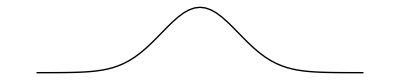

```mathematica
Show[Graphics[graphline]]
```

In fact, this line is a polygonal curve, but the corners are too close to be visible at this magnification.

The colors will be obtained by generating polygons which are filled with the appropriate color. Assume that we are given n+1 function values f[x_0], f[x_1], ... f[x_n]. From these n+1 values we can generate n polygons, where the k-th polygon is given by the points x_k, f[x_k], f[x_(k+1)], and x_(k+1)(k=0,..n-1). In a conventional programming language, one would think to generate the list of polygons with a sort of do-loop. In Mathematica it is much more effective to apply list operations. We first generate an auxiliary list of zero values

```mathematica
nullv = Table[0,{Length[xvalues]}];
```

The n-1 points (x_k,0) for k=0 .. n on the x-axis are obtained by

```mathematica
xpoints = {xvalues, nullv}//Transpose;
```

Next we form the list of points with coordinates (x_k,f[x_k])

```mathematica
ypoints = {xvalues, absvals}//Transpose;
```

Now, this is a list of corner points for the polygons. The command Drop[list,±1] removes either the first or the last element of a list.

```mathematica
cornerpoints = {Drop[xpoints,-1], Drop[ypoints,-1], Drop[ypoints,1], Drop[xpoints,1]}//Transpose;
```

```mathematica
Short[cornerpoints,3]
```

{{{-3.,0},{-3.,0.00012341},{-2.9,0.00022263},{-2.9,0}},{{-2.9,0},{-2.9,0.00022263},{-2.8,0.000393669},{-2.8,0}},«56»,{{2.8,0},{2.8,0.000393669},{2.9,0.00022263},{2.9,0}},{{2.9,0},{2.9,0.00022263},{3.,0.00012341},{3.,0}}}

The list of polygons is formed by mapping the command Polygon on the list of corner points.

```mathematica
polylist = Map[Polygon, cornerpoints];
```

Finally, we combine the color directives from the list hue with each polygon

```mathematica
coloredpolys = {Drop[huevals,-1],polylist}//Transpose;
```

Lets have a look at this:

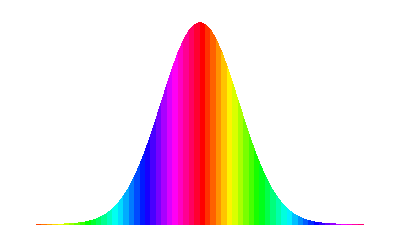

```mathematica
Show[Graphics[coloredpolys],AspectRatio->(1/GoldenRatio)]
```

We can combine this with the line of the curve:

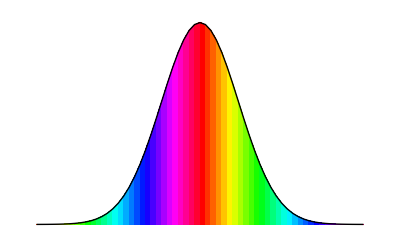

```mathematica
Graphics[{coloredpolys,graphline},AspectRatio->(1/GoldenRatio)]
```

We combine everything into a single command. This can be done using a Module.

```mathematica
fillit[xvars_,hues_,values_] :=
   Module[{nullv,xpts,valpts,lines,fills},
      nullv = Table[0,{Length[xvars]}];
		xpts = {xvars,nullv}//Transpose;
      valpts = {xvars,values}//Transpose;
		lines = Line[valpts];
      fills =
         {Drop[hues,-1],
             Map[Polygon,
					    { Drop[xpts,-1], Drop[valpts,-1], Drop[valpts, 1],Drop[xpts, 1]
                          }//Transpose
             ]
         }//Transpose;
      Show[Graphics[ {fills,lines} ],AspectRatio->(1/GoldenRatio)]
   ]
```

Let us test this command with a small list:

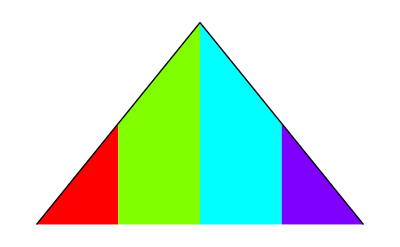

```mathematica
fillit[{1,2,3,4,5}, Hue/@{0,.25,.5,.75,1}, {0,1,2,1,0}]
```

### Phase-colored plot

We can easily use the command fillit to define a useful plot command for a list of complex numbers:

```mathematica
ListArgColorPlot[list_List] :=
   Module[{xvars,hues,values},
         xvars	= Range[Length[list]];
         hues	= Hue[Arg[#]/(2 Pi)]& /@ list;
         values	= Abs[list];
         fillit[xvars,hues,values]
         ]
```

```mathematica
f[x_] := Tan[x + 0.3 I]
```

```mathematica
yvalues = Table[f[x],{x,-5.,5.,0.01}];
```

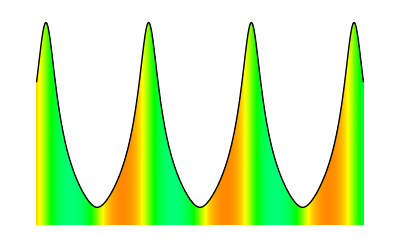

```mathematica
ListArgColorPlot[yvalues]
```

In Mathematica 6 we can use ColorFunction to color the graphics as desired, however, antialiasing does not work (but should be possible to get it working).

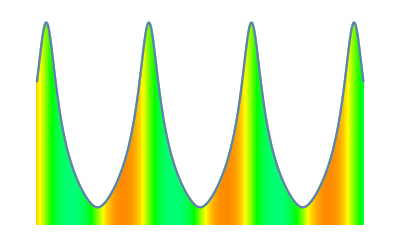

```mathematica
ListArgColorPlot6[list_]:=With[{intfun=Interpolation@list},Style[ListLinePlot[Abs@list,Filling->Bottom,ColorFunctionScaling->False,
Epilog->(FF=First[ListLinePlot[Abs@yvalues]]),Axes->False,
ColorFunction:>Function[{x,y},(Hue@(Mod[Arg[intfun[x]]/(2Pi),1]))]],
Antialiasing->True]];

ListArgColorPlot6@yvalues
```

## The package VQM`ArgColorPlot

The (non-standard) package VQM`ArgColorPlot provides additional functionality

```mathematica
Needs["VQM`ArgColorPlot`"]
```

All symbols defined by the VQM packages start with the letter "Q". In particular, the package implements QListArgColorPlot which corresponds to the command ListArgColorPlot defined above. But the command defined in the package accepts the standard options:

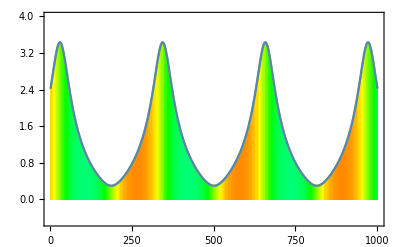

```mathematica
yvalues = Table[Tan[x + 0.3 I],{x,-5.,5.,0.01}];
QListArgColorPlot[yvalues, Frame->True, Axes->{True,False},PlotRange->{-.5,4}]
```

There is a variant which corresponds to Plot

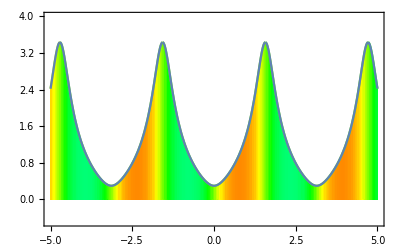
{0.046875,-Graphics-}

```mathematica
Timing@QArgColorPlot[Tan[x + 0.3 I], {x,-5,5}, Frame->True, Axes->{True,False},
PlotRange->{-.5,4}]
```

Further documemtation is available via Mathematica's Help Browser, provided the VQM packages are properly installed.

Moreover, you can get help in the usual way:

```mathematica
?QArgColorPlot
```

QArgColorPlot[f[x],{x,x0,x1},opts] is used
like the usual Plot command. It gives a two-dimensional plot
of a complex-valued function f of a single real variable x
in the range {x0,x1}.
The plot shows the curve Abs[f] with area between the curve
and the x-axis colored by Hue[Arg[f[x]]/(2 Pi)].
The default options of Plot are changed to Axes->{True,None},
Frame->True. Package: VQM`ArgColorPlot`

```mathematica
Options[QArgColorPlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,Compiled→True,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,Epilog→{},Filling→None,FillingStyle→Automatic,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→True,LabelingFunction→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,Opacity→1,PlotLabel→None,PlotLabels→None,PlotLayout→Overlaid,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},QBottomLine→0,QBrightness→1,QPlotDown→False,QSaturation→1,QShiftPlot→0,QSquared→False,RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},DisplayFunction:>$DisplayFunction,FormatType:>TraditionalForm,PerformanceGoal:>$PerformanceGoal,PlotTheme:>$PlotTheme}

```mathematica
?QSaturation
```

Option for QArgColorPlot. QSaturation->s causes the colors
in the plot to appear at saturation s. Default value is 1. Package: VQM`ArgColorPlot`

## Examples for using the ArgColorPlot package

This example shows a complex-valued Gaussian function.

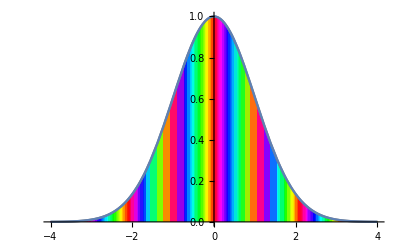

```mathematica
QArgColorPlot[ⅇ^(-ⅈ 6 x-x^2/2),{x,-4,4}]
```

Most of the options for ListLinePlot can be used also for QArgColorPlot. In addition, we can influence the Saturation and the Brightness of the colors for the complex phase:

```mathematica
tmp=Manipulate[QArgColorPlot[ⅇ^(-ⅈ 6 x-x^2/2),{x,-4,4},PlotStyle->{Thickness[th],GrayLevel[0.5]},QSaturation->sat,QBrightness->bri,PlotRange->{-0.2,1.2},Frame->True,Axes->{True,False}],
{{sat,0.5,"saturation"},0,1},
{{bri,0.7,"brightness"},0,1},
{{th,0.025,"thickness"},0.001,0.05},
Initialization:>Needs["VQM`"]
]
```

Next, we illustrate the usage of QListArgColorPlot. First, we create a list of complex numbers.

```mathematica
mytab=Table[Sin[π x] ⅇ^(2 ⅈ π x),{x,-2,2,0.01}];
```

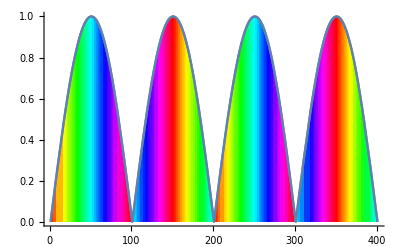

```mathematica
QListArgColorPlot[mytab]
```

If, like here, the complex values come from the discretization of a function of a real variable x, we want to have x-values on the horizontal axis, and not the index of the complex list. This can be done with the option QHorizontalRange which specifies the range of x-values on the horizontal axis:

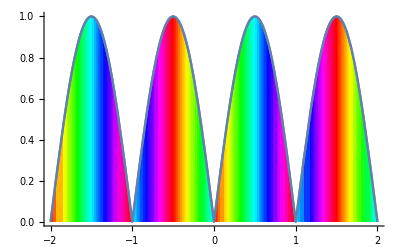

```mathematica
QListArgColorPlot[mytab,Axes->True,QHorizontalRange->{-2,2}]
```

Here is another method to achieve a similar result:

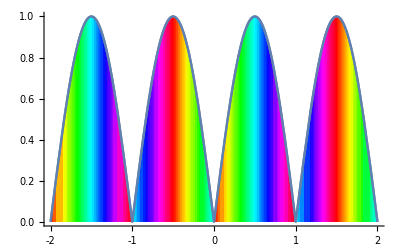

```mathematica
QListArgColorPlot[mytab, Axes→True, Ticks->{QNiceTicks[-2.,2.,0.01],Automatic}]
```

We can also plot a part of the list, corresponding, for example, to the values in the sub-interval {-1,0} of the horizontal range {-2,2}:

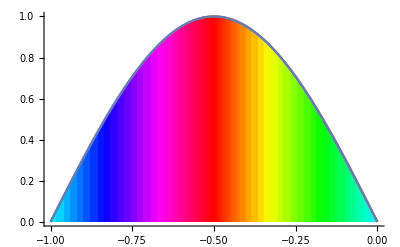

```mathematica
QListArgColorPlot[mytab,Axes->True,QHorizontalRange->{{-2,2},{-1,0}}]
```

If the "sub-interval" is larger than the horizontal range, the list will be padded with zeros:

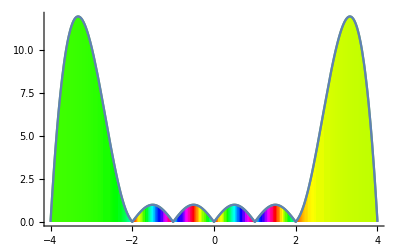

```mathematica
QListArgColorPlot[mytab,Axes->True,QHorizontalRange->{{-2,2},{-4,4}}]
```

If you want to combine a phase-colored plot with an ordinary plot of another function, you can use QCombinedPlot:

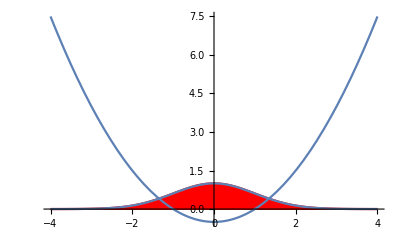

```mathematica
QCombinedPlot[{Exp[-x^2/2],x^2/2-1/2},{x,-4,4}]
```

There is also a "ListPlot"-version of QCombinedPlot, where a list of complex values is plotted together with an ordinary function:

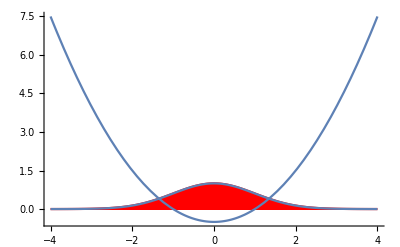

```mathematica
mytab=Table[Exp[-x^2/2],{x,-4,4,0.1}];
QListCombinedPlot[{mytab,x^2/2-1/2},{x,-4,4}]
```

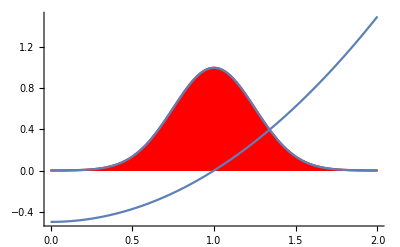

```mathematica
QListCombinedPlot[{mytab,x^2/2-1/2},{x,0,2}]
```

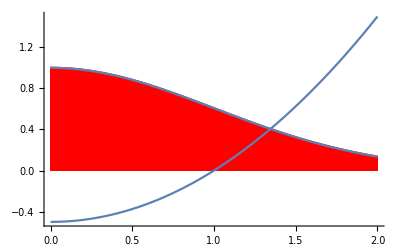

```mathematica
QListCombinedPlot[{mytab,x^2/2-1/2},{x,0,2},QHorizontalRange->{-4,4}]
```

Normally, in QArgColorPlot, the range between the x-axis and the graph of the function is filled with a color corresponding to the phase. But we can also use another horizontal line at height y=y0 by using the option QBottomLine->y0:

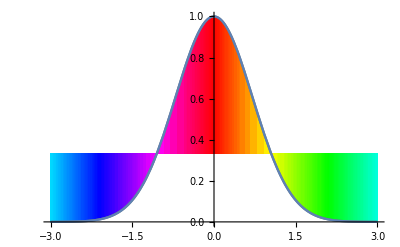

```mathematica
QArgColorPlot[Exp[I x - x^2],{x,-3,3}, QBottomLine→1/3]
```

This is useful, if we want to combine several ArgColorPlots in the same graphics:

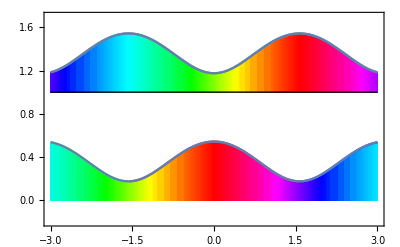

```mathematica
Show[QArgColorPlot[Sin[x+ⅈ],{x,-3,3},QBottomLine->1,Epilog->Line[{{-3,1},{3,1}}]],QArgColorPlot[Cos[x+ⅈ]-ⅇ^(ⅈ Arg[Cos[x+ⅈ]]),{x,-3,3}],PlotRange->{-0.2,1.7},Frame->True]
```

Some more options for use with QArgColorPlot:

QSquared->True plots the square of the curve instead of the absolute value:

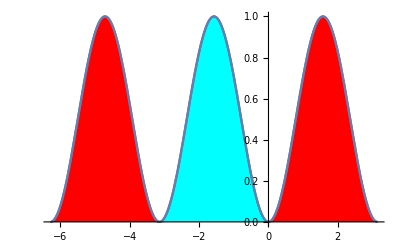

```mathematica
QArgColorPlot[Sin[x],{x,-2Pi,Pi}, QSquared->True]
```

QShiftPlot->number performs a vertical shift of the whole plot by number.

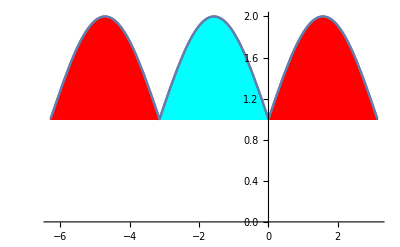

```mathematica
QArgColorPlot[Sin[x],{x,-2Pi,Pi}, QShiftPlot->1, PlotRange->{0,2}]
```

QPlotDown->True lets the whole plot appear uside down.

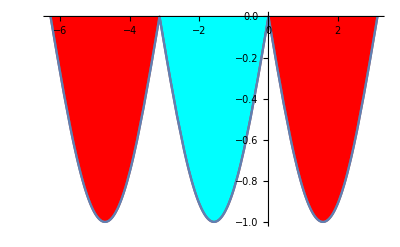

```mathematica
QArgColorPlot[Sin[x],{x,-2Pi,Pi}, QPlotDown->True]
```

In quantum mechanics, a ℂ^2-valued functions is called a spinor function. The ArgColorPlot has a method to plot such functions by combining QArgColorPlots of the two component-functions. By default, the second component is plotted upside down and with less saturation:

RM: QSpinorPlot does not add black boundary-lines for the second component. OK?

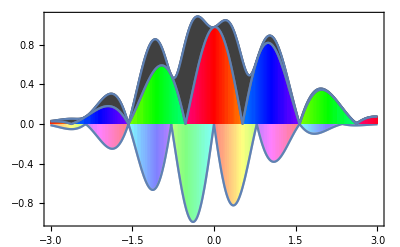

```mathematica
spinorfunction[x_]:={Cos[3 x] ⅇ^(-1/3 (x-1/4)^2+ⅈ x),Sin[4 x] ⅇ^(-1/2 (x+1/4)^2+2 ⅈ x)};
QSpinorPlot[Evaluate[spinorfunction[x]],{x,-3.,3.},PlotRange->All,Frame->True,Axes->{True,False}]
```

Like the other commands, this command accepts options and allows a combination with an ordinary plot

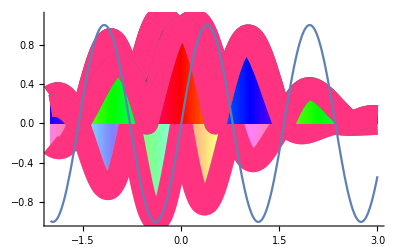

```mathematica
spinorlist=Table[{x,spinorfunction[x]},{x,-3,3,0.1}];
QListSpinorCombinedPlot[{spinorlist,Sin[4 x]},{x,-2,3},PlotRange->All,QCurveStyle->{RGBColor[1,0.7,0.9],Thickness[0.03]},PlotStyle->{RGBColor[1,0.2, 0.5],Thickness[0.04]}]
```

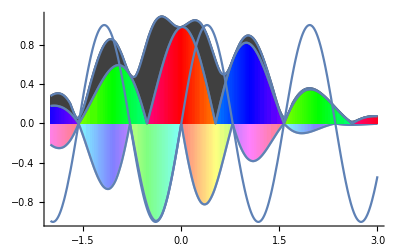

```mathematica
spinorlist=Table[{x,spinorfunction[x]},{x,-3,3,0.1}];
QListSpinorCombinedPlot[{spinorlist,Sin[4 x]},{x,-2,3},PlotRange->All,QCurveStyle->{RGBColor[1,0.7,0.9],Thickness[0.03]}]
```